```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*swarmplot*)
intervalInverse[Interval[]]:=Interval[{-Infinity,Infinity}]
intervalInverse[Interval[int__]]:=Interval@@Partition[Replace[Flatten[{int}],{{-Infinity,mid___,Infinity}:>{mid},{-Infinity,mid__}:>{mid,Infinity},{mid__,Infinity}:>{-Infinity,mid},{mid___}:>{-Infinity,mid,Infinity}}],2]

intervalComplement[a_Interval,b__Interval]:=IntervalIntersection[a,intervalInverse@IntervalUnion[b]]
(*data is assumed to be a sorted vector of numbers*)beeswarm[data_,radius_]:=Module[{points,left,right,int},points={};
Do[int=Interval@@Cases[points,{x_,y_}/;y>pt-radius:>x+{-1,1} Sqrt[radius^2-(pt-y)^2]];
right=Min[intervalComplement[Interval[{0,Infinity}],int]];
left=Max[intervalComplement[Interval[{-Infinity,0}],int]];
AppendTo[points,{If[right<-left,right,left],pt}],{pt,data}];
points]
Options[beeswarmPlot]=Join[Options[Graphics],{PlotStyle->Automatic}];

SetOptions[beeswarmPlot,Frame->True];
SetOptions[beeswarmPlot,FrameTicks->{None,Automatic}];

beeswarmPlot[data_?(VectorQ[#,NumericQ]&),radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=beeswarmPlot[{data},radius,opt]
beeswarmPlot[data:{__?(VectorQ[#,NumericQ]&)},radius:(_?NumericQ|Automatic):Automatic,opt:OptionsPattern[]]:=Module[{r,order,flatData,colours,colfun},(*generate colour indices and sort them together with the data*)flatData=Flatten[data];
order=Ordering[flatData];
colours=Flatten@Table[ConstantArray[i,Length[data[[i]]]],{i,Length[data]}];
flatData=flatData[[order]];
colours=colours[[order]];
(*automatic radius selection*)r=If[radius===Automatic,4 Mean@Differences[flatData],2 radius];
(*handle the PlotStyle option*)colfun=With[{ps=OptionValue[PlotStyle]},Switch[ps,Automatic,ColorData[1],_List,Function[i,ps[[Mod[i,Length[ps],1]]]],_,ps&]];
(*call the packing function and build the graphics using the result*)Graphics[MapThread[{colfun[#2],Disk[#1,0.95 r/2]}&,{beeswarm[flatData,r],colours}],Sequence@@FilterRules[{opt},Options[Graphics]],Frame->OptionValue[Frame],FrameTicks->OptionValue[FrameTicks]]]
```

```mathematica
(*plot parameters*)
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
SwarmCol = {"#94c33a","#9952df","#dc7124","#593193","#56b16c","#cf5aba","#657ade","#aa9040","#bc002d","#8686ce","#7d3f00"};
```

```mathematica
NonSensorColor=hexToRGB["#bf00bf"];
SensorColor=hexToRGB["#5db6be"];
MarkerSensor = Graphics[{SensorColor,Disk[]}];
MarkerNonSensor = Graphics[{NonSensorColor,Disk[]}];
```

## Import data

```mathematica
OrderMostRepeat=Import["General_data/OrderRepeatSP.mx"];
Detect=Import["General_data/DetectSP.mx"];
Detect0=Import["General_data/DetectSP0.mx"];
SensorScore=Import["General_data/SensorsRepeatSP.mx"];
SetSizeS = Import["General_data/NumberOfSensorsS.mx"];
SetSizeP = Import["General_data/NumberOfSensorsP.mx"];
SetSize = Join[SetSizeS, SetSizeP];
```

## Best EW score for different ratios R_f

data

```mathematica
DetectMost10= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.1]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost15= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.15]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost20= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.2]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost25= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.25]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost30= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.3]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost35= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.35]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost40= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.4]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost45= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.45]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost50= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.5]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost55= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.55]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost60= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.6]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost65= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.65]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost70= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.7]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost75= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.75]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost80= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.8]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost85= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.85]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost90= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.9]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost95= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]*.95]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost100= Table[orderM = OrderMostRepeat[[i]][[1;;Floor[SetSize[[i]]]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost105= Table[orderM = OrderMostRepeat[[i]][[1;;Ceiling[SetSize[[i]]*1.05]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
DetectMost110= Table[orderM = OrderMostRepeat[[i]][[1;;Ceiling[SetSize[[i]]*1.1]]];
Detect[[i]][[orderM]], {i,Length[OrderMostRepeat]}];
```

```mathematica
DetectSizeProp = Table[
{Max[DetectMost10[[i]]],
Max[DetectMost15[[i]]],
Max[DetectMost20[[i]]],
Max[DetectMost25[[i]]],
Max[DetectMost30[[i]]],
Max[DetectMost35[[i]]],
Max[DetectMost40[[i]]],
Max[DetectMost45[[i]]],
Max[DetectMost50[[i]]],
Max[DetectMost55[[i]]],
Max[DetectMost60[[i]]],
Max[DetectMost65[[i]]],
Max[DetectMost70[[i]]],
Max[DetectMost75[[i]]],
Max[DetectMost80[[i]]],
Max[DetectMost85[[i]]],
Max[DetectMost90[[i]]],
Max[DetectMost95[[i]]],
Max[DetectMost100[[i]]],
Max[DetectMost105[[i]]],
Max[DetectMost110[[i]]]}/Max[Detect[[i]]],{i,Length[DetectMost10]-1}];
DelInf = Table[DeleteCases[DetectSizeProp[[All,i]],-∞],{i,1,21,2}];
Prop1 =Table[pos1=Flatten[Position[DelInf[[i]],_?(#>= 1&)]];
len = Length[pos1];
If[len>11,DelInf[[i]][[pos1[[11;;len]]]]=1.04];
If[len>22,DelInf[[i]][[pos1[[22;;len]]]]=1.08];
If[len>32,DelInf[[i]][[pos1[[32;;len]]]]=1.12];
len/Length[DelInf[[i]]],{i,11}];
```

```mathematica
N[Prop1]
```

{0.290323,0.333333,0.431818,0.521739,0.591837,0.632653,0.632653,0.632653,0.693878,0.76,0.84}

build plot

```mathematica
DelInf[[10]]
```

{1.,0.483870967741935541,1.,0.5999999999999999,1.,0.631578947368420773,0.043478260869565056,1.,0.88461538461538473,0.499999999999999878,1.,1.,0.882352941176470562,1.,1.,0.91304347826086955,0.882352941176470562,0.739130434782608651,0.157894736842105091,0.299999999999999612,1.,0.40000000000000016,0.2,0.249999999999999903,1.,0.222222222222222318,0.47619047619047628,1.04,0.869565217391304157,0.944444444444444636,1.04,1.04,1.04,0.708333333333333401,1.04,1.04,0.592592592592592561,0.599999999999999844,1.04,0.708333333333333401,1.04,1.04,1.04,0.86666666666666663,1.04,0.66666666666666684,0.722222222222222318,0.619047619047618977,1.04,0.714285714285714233}

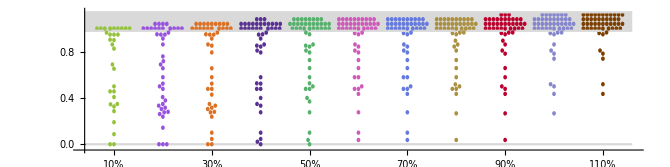

```mathematica
widthS =.02;
Bees=Graphics[{First@beeswarmPlot[DelInf[[1]],widthS,PlotStyle->hexToRGB[SwarmCol[[1]]]],Translate[First@beeswarmPlot[DelInf[[2]],widthS,PlotStyle->hexToRGB[SwarmCol[[2]]]],{0.5,0}],Translate[First@beeswarmPlot[DelInf[[3]],widthS,PlotStyle->hexToRGB[SwarmCol[[3]]]],{1,0}],
Translate[First@beeswarmPlot[DelInf[[4]],widthS, PlotStyle->hexToRGB[SwarmCol[[4]]]],{1.5,0}],
Translate[First@beeswarmPlot[DelInf[[5]],widthS, PlotStyle->hexToRGB[SwarmCol[[5]]]],{2,0}],
Translate[First@beeswarmPlot[DelInf[[6]],widthS,PlotStyle->hexToRGB[SwarmCol[[6]]]],{2.5,0}],
Translate[First@beeswarmPlot[DelInf[[7]],widthS,PlotStyle->hexToRGB[SwarmCol[[7]]]],{3,0}],
Translate[First@beeswarmPlot[DelInf[[8]],widthS,PlotStyle->hexToRGB[SwarmCol[[8]]]],{3.5,0}],
Translate[First@beeswarmPlot[DelInf[[9]],widthS,PlotStyle->hexToRGB[SwarmCol[[9]]]],{4,0}],
Translate[First@beeswarmPlot[DelInf[[10]],widthS,PlotStyle->hexToRGB[SwarmCol[[10]]]],{4.5,0}],
Translate[First@beeswarmPlot[DelInf[[11]],widthS,PlotStyle->hexToRGB[SwarmCol[[11]]]],{5,0}]
},Frame->False];
band2 = ListPlot[{{-.3,0},{5.3,0}},PlotStyle->{{LightGray}}, Joined->True];
band1= ListPlot[{{{-.3,.98},{5.3,.98}},{{-.3,1.14},{5.3,1.14}}},PlotStyle->{{LightGray}}, Joined->True,Filling-> {1->{{2},{Opacity[0.15
]}}},Ticks->{{{0,"10%"},{.5,"20%"},{1,"30%"},{1.5,"40%"},{2,"50%"},{2.5,"60%"},{3,"70%"},{3.5,"80%"},{4,"90%"},{4.5,"100%"},{5,"110%"}},{{0,"0.0"},{.2,".02"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1.06,"1.0"}}},PlotRange->{{-.3,5.3},{-.05,1.15}}];
BeeSwarmAll = Show[band1,band2,Bees,AspectRatio->1/4,AxesOrigin->{-.3,-.05}]
```

## Sensor Score - EW Score density distribution

```mathematica
dScore = Table[Detect[[i]]/Max[Detect[[i]]],{i,Length[Detect]}]; (*EW-score with full competition*)
dScore0 = Table[Detect0[[i]]/Max[Detect0[[i]]],{i,Length[Detect0]}]; (*EW-score with no competition*)
FSensorScore=Flatten[SensorScore];
FDetectScore = Flatten[dScore]; (*EW-score with full competition (flattened) *)
FDetectScore0 = Flatten[dScore0];
PairDetectSensor = Transpose@{FDetectScore,FSensorScore};
PairDetectSensorm = Transpose@{-1*Flatten[dScore ],Flatten[SensorScore]};
```

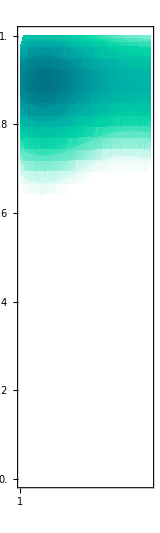
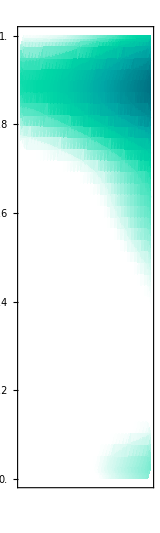
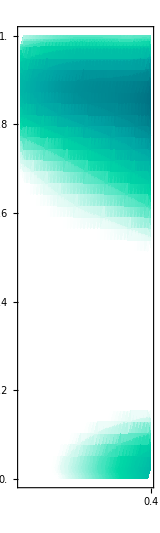
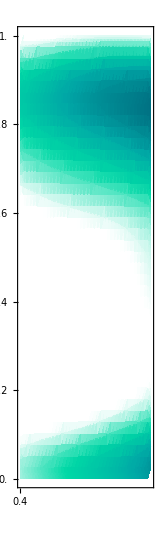
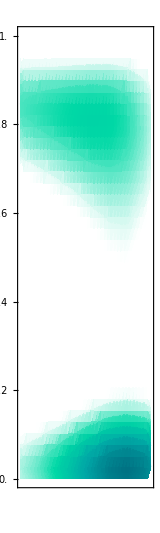

```mathematica
Table[SmoothDensityHistogram[PairDetectSensorm,Automatic, "Intensity",ColorFunction->(Blend[{White,White, RGBColor[0, 0.85, 0.65],RGBColor[0, 0.65, 0.65],RGBColor[0, 0.44, 0.51]},Rescale[#,{0,1}]]&),FrameTicks->{{Range[0,1,0.2],None}, {{{-1,1},{-.9,.9},{-.8,.8},{-.7,.7}, {-.6,.6},{-.5,.5}, {-.4,.4},{-.3,.3}, {-.2,.2},{-.1,.1},{0,0}},None}},FrameTicksStyle->12,
ColorFunctionScaling->True,
 Mesh->6,
 PlotLegends->Placed[Automatic,Above],PlotRange->{{i,i+.2},{0,1}},AspectRatio->5/1.5,ImageSize->{160,350}],{i,{-1,-.8,-.6,-.4,-.2}}]
```

## probability of finding a given early - warning score

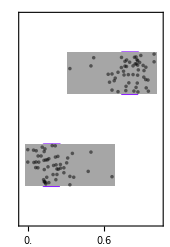

```mathematica
ClearAll[cef2]
bins={0,0.5,1};
datatemp=Table[
HistogramList[d,{bins},"Probability"]⟦2⟧
,{d, dScore}];
cef2={
EdgeForm[],FaceForm[],ChartElementData["BoxWhisker"][##]/.{l_Line:>{RGBColor[0.55, 0.13, 1],l},GrayLevel[0]->RGBColor[0.55, 0.13, 1]},ChartElementData["PointDensity","PointStyle"->Directive[Opacity[0.5],PointSize[0.015],Black]][##]}&;

fig1=BoxWhiskerChart[Reverse@Transpose@datatemp,
Frame->True,
ChartElementFunction->cef2,
AspectRatio->0.8GoldenRatio,
FrameTicksStyle->12,
FrameTicks->{{All,All},{Range[0,1,0.2],None}},
ChartStyle->Directive[EdgeForm[Black], Gray],
ImageSize->170,
BarOrigin->Left];

options={{
{"MedianMarker",1,None},
{"MeanMarker",1,Directive[Thickness[.01],RGBColor[0.55, 0.13, 1]]},
{"Fences",1,Directive[Thickness[.01],RGBColor[0.55, 0.13, 1]]},
{"Whiskers",Directive[Thickness[.01],CapForm["Butt"],RGBColor[0.55, 0.13, 1]]}},
ChartStyle->Directive[EdgeForm[{RGBColor[0.55, 0.13, 1],Thickness[0.01]}], White],
ChartElementFunction->ChartElementDataFunction["BoxWhisker"]};

fig2=BoxWhiskerChart[Reverse@Transpose@datatemp,##&@@options,
Frame->True,
AspectRatio->0.9GoldenRatio,
FrameTicksStyle->12,
FrameTicks->{{All,All},{Range[0,1,0.2],None}},
ImageSize->170,
BarOrigin->Left];

fig3 = Show[{fig2, fig1}]
```